```mathematica
Integrate[3*m*v^-(3*m+1),{v,v0,v1},Assumptions->{m>0,v>0,v0>0,v1>0}]
```

ConditionalExpression[v0^(-3 m)-v1^(-3 m), v0≠v1]

```mathematica
FullSimplify[Integrate[x^(1/a)*(1-x)^a,{x,0,1},Assumptions->{x>0,a>0,x0≥ 0,x1≥ 0,x0≤ 1,x1≤ 1}]]
```

(Gamma[1+1/a] Gamma[1+a])/Gamma[2+1/a+a]

```mathematica
dg[m_]:=2.601*10^-11*m^-1.9
```

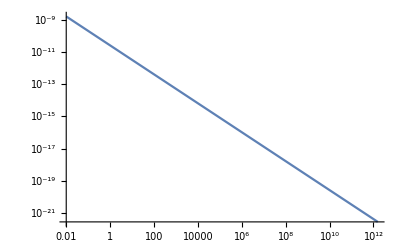

```mathematica
LogLogPlot[m*dg[m],{m,0.01,1.57*10^12}]
```

```mathematica
Integrate[m*dg[m],{m,0.01,x}]
```

ConditionalExpression[2.601×10^-11 (-6.30957+10. x^0.1), Re[x]>6.×10^-23||x∉ℝ]

```mathematica
Integrate[Sin[x],{x,0,Pi/2}]
```

1

```mathematica
FullSimplify[Integrate[Exp[-(x-x0)^2/(a^2)],{x,B0,B1}]]
```

1/2 a √π (-Erf[(B0-x0)/a]+Erf[(B1-x0)/a])

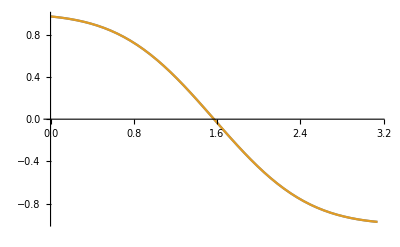

```mathematica
Plot[{Erf[(π-2 x0)/(2 a)]/.a->1,-Erf[(2 x0-Pi)/(2 a)]/.a->1},{x0,0,Pi}]
```

```mathematica
G[x_]:=1/(2*Pi)*(3*a/(2*Pi-3*a)*Cos[x]+1)
```

```mathematica
Integrate[G[x],{x,b0,b1}]
```

(-b0+b1+(3 a (-Sin[b0]+Sin[b1]))/(-3 a+2 π))/(2 π)

```mathematica
Simplify[(-b0+b1+(3 a (-Sin[b0]+Sin[b1]))/(-3 a+2 π))/(2 π)]
```

(-b0+b1+(3 a (-Sin[b0]+Sin[b1]))/(-3 a+2 π))/(2 π)

```mathematica
D[Cos[x],x]
```

-Sin[x]

```mathematica
Integrate[x^(1/a)*(1-x)^a,{x,x0,x1}]
```

ConditionalExpression[-Beta[x0,1+1/a,1+a]+Beta[x1,1+1/a,1+a], ]

```mathematica
Integrate[Exp[-(x-x0)^2/a^2]*Sin[x],{x,0,Pi/2}]
```

-1/4 a ⅇ^(-a^2/4-ⅈ x0) √π (Erfi[(a^2-ⅈ π+2 ⅈ x0)/(2 a)]+ⅇ^(2 ⅈ x0) (Erfi[(a^2+ⅈ (π-2 x0))/(2 a)]-Erfi[a/2-(ⅈ x0)/a])-Erfi[a/2+(ⅈ x0)/a])

```mathematica
NIntegrate[x^(1/a)*(1-x)^a,{x,x0,x1}]/.{a->1, x0->0.1, x1->0.2}
```

0.0126667

```mathematica
deven[x_,a_,b_,m_]:=m*(b-m)*x/((a+2*m-1)*(a+2*m))
dodd[x_,a_,b_,m_]:=-(a+m)*(a+b+m)*x/((a+2*m)*(a+2*m+1))
```

```mathematica
Manipulate[Plot[{deven[x0,1,1,x],dodd[x0,1+1/5,1+5,x]},{x,0,100},PlotRange->All],{x0,0,1}]
```

```mathematica
Beta[0.695,2.01, 3.2]
```

0.0682195

```mathematica
NumberForm[0.36150964028670585,16]
```

0.3615096402867058

```mathematica
Series[Beta[a+1,1/a+1],{a,0, 3},Assumptions->a>0]
```

a+(-1-EulerGamma+Log[a]) a^2+1/12 (-6+12 EulerGamma+6 EulerGamma^2+π^2-12 Log[a]-12 EulerGamma Log[a]+6 Log[a]^2) a^3+O[a]^4

```mathematica
F[x_,a_]:=(1-Cos[x])^(Sqrt[(1-Cos[a])/Cos[a]])*Cos[x]^(Sqrt[Cos[a]/(1-Cos[a])])/Beta[1+(Sqrt[Cos[a]/(1-Cos[a])]),1+1/(Sqrt[Cos[a]/(1-Cos[a])])]
```

```mathematica
Manipulate[Plot[F[x*Pi/180,a*Pi/180],{x,0,90},PlotRange->All],{a,0,90}]
```

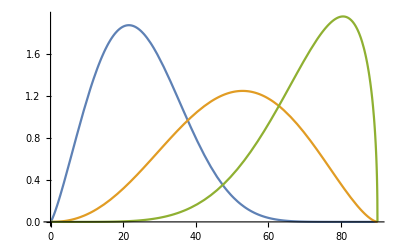

```mathematica
Plot[{F[x*Pi/180,10*Pi/180]*Sin[x*Pi/180],F[x*Pi/180,45*Pi/180]*Sin[x*Pi/180],F[x*Pi/180,80*Pi/180]*Sin[x*Pi/180]},{x,0,90},PlotRange->All]
```

```mathematica
F1[x_,a_]:=x^(1/(Sqrt[Cos[a]/(1-Cos[a])]))*(1-x)^(Sqrt[Cos[a]/(1-Cos[a])])/Beta[1+(Sqrt[Cos[a]/(1-Cos[a])]),1+1/(Sqrt[Cos[a]/(1-Cos[a])])]
```

```mathematica
Integrate[F1[x,a],{x,0,1}]
```

1

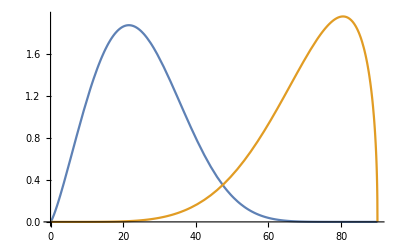

```mathematica
Plot[{F1[1-Cos[x*Pi/180],10*Pi/180]*Sin[x*Pi/180],F1[1-Cos[x*Pi/180],80*Pi/180]*Sin[x*Pi/180]},{x,0,90}]
```

```mathematica
Integrate[F[x,a]*Sin[x],{x,0,Pi/2},Assumptions->a>0]
```

$Aborted

```mathematica
Solve[D[(1-Cos[x])^(1/a)*Cos[x]^a,x]==0,x]
```

{{x→-ArcSec[(1+a^2)/a^2]},{x→ArcSec[(1+a^2)/a^2]}}

```mathematica
Integrate[x^(1/a)*(1-x)^a,{x,x0,x1},Assumptions->{a>0,x0≥0,x1>0,x≥0,x0<1,x1≤1}]
```

ConditionalExpression[-Beta[x0,1+1/a,1+a]+Beta[x1,1+1/a,1+a], x0>0&&x0<x1<1]

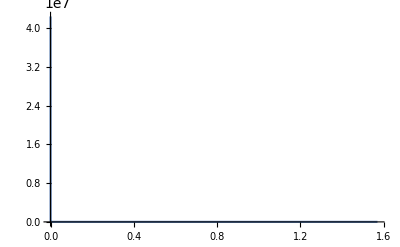

```mathematica
Plot[Sqrt[Cos[a]/(1-Cos[a])],{a,0,Pi/2},PlotRange->Full]
```

```mathematica
Series[Beta[x,1+1/a,1+a],{a,Infinity,2}]
```

Beta[x,1+1/a,1+a]

```mathematica
Integrate[Normal[Series[x^(1/a)*(1-x)^a,{a,0,1}]],{x,x0,x1},Assumptions->{a>0,x0≥0,x1>0,x≥0,x0<1,x1≤1}]
```

ConditionalExpression[(-a^3 x0^(2+1/a) Hypergeometric2F1[1,2+1/a,3+1/a,x0]+a^3 x1^(2+1/a) Hypergeometric2F1[1,2+1/a,3+1/a,x1]-a (1+2 a) (x0^(1+1/a)-x1^(1+1/a)+a x0^(1+1/a) Log[1-x0]-a x1^(1+1/a) Log[1-x1]))/((1+a) (1+2 a)), x0≠x1&&x0>0]

```mathematica
Series[Pochhammer[2+1/a,n]/Pochhammer[3+1/a,n],{a,0,1},Assumptions->{a>0,n>0}]
```

1-n a+O[a]^(3/2)

```mathematica
Beta[1+1/1.553773974,1+1.553773974]
```

0.160703

```mathematica
Beta[0,1,1]
```

0

```mathematica
Series[Tan[D]^2*(Csc[D]-1),{D,0,3}]
```

D-D^2+(5 D^3)/6+O[D]^4

```mathematica
D[(1-Cos[x])^(1/a)*Cos[x]^a*Sin[x],x]==0
```

(1-Cos[x])^(1/a) Cos[x]^(1+a)-a (1-Cos[x])^(1/a) Cos[x]^(-1+a) Sin[x]^2+((1-Cos[x])^(-1+1/a) Cos[x]^a Sin[x]^2)/a==0

```mathematica
Solve[D[(x)^(1/a)*(1-x)^a,x]==0,x]
```

{{x→1/(1+a^2)}}

```mathematica
Series[Cos[x],{x,0,3}]
```

1-x^2/2+O[x]^4

```mathematica
FullSimplify[Normal[Series[(Cos[2*r]-Cos[D+r]^2*Cos[r]^2)/(1-Cos[D+r]^2*Cos[r]^2),{D,0,0}]]]
```

1-4/(3+Cos[2 r])

```mathematica
FullSimplify[(Cos[r]^4-Cos[2 r])/(-1+Cos[r]^4)]
```

1-4/(3+Cos[2 r])

```mathematica
FullSimplify[(2 D Cos[r]^3 (-1+Cos[2 r]) Sin[r])/((-1+Cos[r]^4)^2)]
```

-(16 D Cos[r]^2 Cot[r])/(3+Cos[2 r])^2

```mathematica
Series[Cos[x],{x,0,3}]
```

1-x^2/2+O[x]^4

```mathematica
Manipulate[Plot[{(1-(Cos[2*r]-Cos[D+r]^2*Cos[r]^2)/(1-Cos[D+r]^2*Cos[r]^2)-2*r^2/Sin[D]^2)/(1-(Cos[2*r]-Cos[D+r]^2*Cos[r]^2)/(1-Cos[D+r]^2*Cos[r]^2))},{D,0.0002,Pi-0.1},PlotRange->All],{r,0.0001,0.1}]
```

```mathematica
Series[ArcCos[-1+A],{A,0,1}]
```

π-√2 √A+O[A]^(3/2)

```mathematica
FullSimplify[(1-Cos[D+r]^2*Cos[r]^2)^2 - (Cos[2*r]-Cos[D+r]^2*Cos[r]^2)^2]
```

Sin[2 r]^2 Sin[D+r]^2

```mathematica
Series[Cos[r],{r,0,2}]
```

1-r^2/2+O[r]^3